# Figures 1BCDE, 2ABC, 3A, S2

### This Mathematica notebook uses pre-processed data from experiments and computer simulations to generate the figures. For data processing, see process_data.nb For pre-processing computer simulations see figures_xxx.nb where xxx = RIF, CIP or STR Notebook testes with Mathematica 14.0 - 14.2

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor

## Some helper functions

### This section also sets some of the plotting options that are used across all figures

```mathematica
SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
SetOptions[{ListPlot,ListLogPlot,ListLinePlot,Histogram},BaseStyle->FontSize->24,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];

(* this is used to remove spikes from OD vs time data that occassionally occur due to bubbles trapped in the OD spectrophotometer *)
Clear[RemoveSpikes]
RemoveSpikes[d_,eps_:0.005]:=Module[{diff=Abs[Differences[d[[All,2]]]]},Select[Table[{d[[i]],If[i<Length[d]-1,If[diff[[i+1]]<eps && diff[[i]]<eps,True,False],If[diff[[i-1]]<eps,True,False]]},{i,Length[d]}],(#[[2]])&][[All,1]]]
```

## RIF Mutation rates from the fluctuation test

### This loads in an Excel spreadsheet containing data for RIF 100 ug/ml for many different strains and experiments carried out on different dates

```mathematica
raw=Import[NotebookDirectory[]<>"Fluctuation_RIF_summary.xlsx","XLSX"];
Length[raw]
Length[#]&/@raw
```

7

{33,47,26,22,26,16,16}

### Multiple columns and sheets are polled together for AD30+EEL02 strains. We do not to use data for MG1655.

```mathematica
sheet={2,2,2,3,3,4};cols={2,4,6,2,4,2};
tmp=Table[{raw[[sheet[[i]],4,cols[[i]]]],raw[[sheet[[i]],4,cols[[i]]+1]],Floor[Select[raw[[sheet[[i]],7;;,cols[[i]]]],(NumberQ[#])&]]},{i,Length[cols]}]
```

{{633.,1.083×10^8,{5,1,48,1,51,5,2,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{326.,1.576×10^8,{0,0,0,0,2,45,8,9,2,9,1,30,4,6,4,17,27,12,6,1}},{296.,1.776×10^8,{0,0,0,0,0,0,0,0,2,26,11,1,6,5,28,4,5,5,20,112}},{636.,1.664×10^8,{0,0,0,0,1,1,3,6,13,42,5,1,1,1,10,4,7,1,4,8}},{556.,1.16×10^8,{0,0,0,0,0,0,0,0,2,3,3,8,3,6,17,34,2,2,1,44}},{1133.,1.×10^9,{6,10,2,28,13,121,10,28,37,7}}}

### This is the function that fits the Lea - Coulson distribution to the experimental distribution of the number of mutants. The function returns (among others) the mean best-fit mutation probability μ.

6.30957×10^-9

maximum at 6.18476×10^-9

General::munfl: Exp[-708.608] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.072] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

129.595

mean μ=6.24159×10^-9

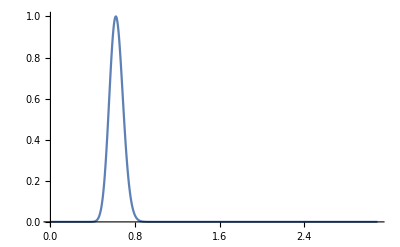

lower 5.05295×10^-9

upper 7.56396×10^-9

{283.547,Null}

```mathematica
Clear[logp]
logp[μ_?NumberQ]:=logp[μ]=Sum[Module[{p,m=tmp[[kk,2]] μ},p[0]=Exp[-m];
p[n_]:=p[n]=m/n Sum[p[i]/(n-i+1),{i,0,n-1}];
Total[Log[p[#]&/@tmp[[kk,3]]]]],{kk,Length[tmp]}];
μguess=Sort[Table[{logp[μ0],μ0}/.μ0->10^x,{x,-11,-7,0.2}]][[-1,2]]
Timing[Module[{fm=FindMaximum[logp[μ],{μ,0.5μguess,1.5μguess}],mumax,norm,dμ,mean,x,tot},mumax=μ/.fm[[2]];Print["maximum at ",mumax];
dμ=mumax/500;
norm=Sum[Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}];
Print[norm];
mean=Sum[μ Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}]/norm;Print["mean μ=",mean];
Print[Plot[Exp[logp[μ]-fm[[1]]],{μ,10^-11,5mumax},PlotRange->All]];
x=0.001mumax;tot=0;While[tot<0.025(norm),tot+=Exp[logp[x]-fm[[1]]];x+=dμ];
Print["lower ",x];
While[tot<0.975(norm),tot+=Exp[Max[-100,logp[x]-fm[[1]]]];x+=dμ];
Print["upper ",x];
]]
```

### The rate that will be used for RIF simulations: μ = 6.2 x 10^- 9

## CIP Mutation rates from the fluctuation test

### This section finds μ for CIP in the same way as the RIF section above.

```mathematica
raw=Import[NotebookDirectory[]<>"Fluctuation_CIP_summary.xlsx","XLSX"];
Length[raw]
Length[#]&/@raw
```

5

{51,46,16,35,26}

```mathematica
sheet={2,3,4};cols={2,2,2};
tmp=Table[{raw[[sheet[[i]],4,cols[[i]]]],raw[[sheet[[i]],4,cols[[i]]+1]],Floor[Select[raw[[sheet[[i]],7;;,cols[[i]]]],(NumberQ[#])&]]},{i,Length[cols]}]
```

{{633.,1.083×10^8,{56,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{1133.,1.×10^9,{1,1,50,1,2,1,5,1,3,0}},{1206.,8.04×10^8,{0,0,0,79,1,1,69,0,3,0,5,4,2,2,23,12,5,0,3,0,1,21,0,2,1,0,0,47,0}}}

1.×10^-9

maximum at 1.16922×10^-9

224.035

mean μ=1.20444×10^-9

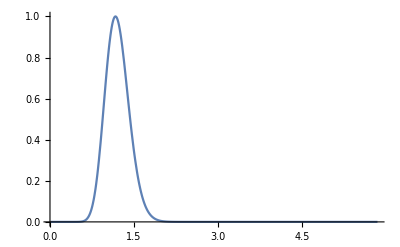

lower 8.26635×10^-10

upper 1.6521×10^-9

{72.1094,Null}

```mathematica
Clear[logp]
logp[μ_?NumberQ]:=logp[μ]=Sum[Module[{p,m=tmp[[kk,2]] μ},p[0]=Exp[-m];
p[n_]:=p[n]=m/n Sum[p[i]/(n-i+1),{i,0,n-1}];
Total[Log[p[#]&/@tmp[[kk,3]]]]],{kk,Length[tmp]}];
μguess=Sort[Table[{logp[μ0],μ0}/.μ0->10^x,{x,-11,-7,0.2}]][[-1,2]]
Timing[Module[{fm=FindMaximum[logp[μ],{μ,0.5μguess,1.5μguess}],mumax,norm,dμ,mean,x,tot},mumax=μ/.fm[[2]];Print["maximum at ",mumax];
dμ=mumax/500;
norm=Sum[Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}];
Print[norm];
mean=Sum[μ Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}]/norm;Print["mean μ=",mean];
Print[Plot[Exp[logp[μ]-fm[[1]]],{μ,10^-11,5mumax},PlotRange->All]];
x=0.001mumax;tot=0;While[tot<0.025(norm),tot+=Exp[logp[x]-fm[[1]]];x+=dμ];
Print["lower ",x];
While[tot<0.975(norm),tot+=Exp[Max[-100,logp[x]-fm[[1]]]];x+=dμ];
Print["upper ",x];
]]
```

### The rate that will be used for CIP simulations: μ = 1.2 x 10^-9

## STR Mutation rates from the fluctuation test

### This section finds μ for STR in the same way as the RIF section above.

```mathematica
raw=Import[NotebookDirectory[]<>"Fluctuation_STR_summary.xlsx","XLSX"];
Length[raw]
Length[#]&/@raw
```

6

{27,71,158,24,26,26}

```mathematica
sheet={2,3};cols={2,2};
tmp=Table[{raw[[sheet[[i]],4,cols[[i]]]],raw[[sheet[[i]],4,cols[[i]]+1]],Floor[Select[raw[[sheet[[i]],7;;,cols[[i]]]],(NumberQ[#])&]]},{i,Length[cols]}]
```

{{633.,1.083×10^8,{5,1,1,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{909.,2.296×10^8,{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

6.30957×10^-10

maximum at 5.75898×10^-10

569.694

mean μ=6.90931×10^-10

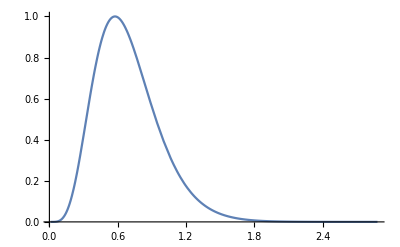

lower 2.55123×10^-10

upper 1.34472×10^-9

{1.0625,Null}

```mathematica
Clear[logp]
logp[μ_?NumberQ]:=logp[μ]=Sum[Module[{p,m=tmp[[kk,2]] μ},p[0]=Exp[-m];
p[n_]:=p[n]=m/n Sum[p[i]/(n-i+1),{i,0,n-1}];
Total[Log[p[#]&/@tmp[[kk,3]]]]],{kk,Length[tmp]}];
μguess=Sort[Table[{logp[μ0],μ0}/.μ0->10^x,{x,-11,-7,0.2}]][[-1,2]]
Timing[Module[{fm=FindMaximum[logp[μ],{μ,0.5μguess,1.5μguess}],mumax,norm,dμ,mean,x,tot},mumax=μ/.fm[[2]];Print["maximum at ",mumax];
dμ=mumax/500;
norm=Sum[Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}];
Print[norm];
mean=Sum[μ Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}]/norm;Print["mean μ=",mean];
Print[Plot[Exp[logp[μ]-fm[[1]]],{μ,10^-11,5mumax},PlotRange->All]];
x=0.001mumax;tot=0;While[tot<0.025(norm),tot+=Exp[logp[x]-fm[[1]]];x+=dμ];
Print["lower ",x];
While[tot<0.975(norm),tot+=Exp[Max[-100,logp[x]-fm[[1]]]];x+=dμ];
Print["upper ",x];
]]
```

### the rate that will be used for STR simulations: μ = 6.9 x 10^-10

## STRmutS Mutation rates from the fluctuation test

### This section finds μ for STR for the mutS strain in the same way as the RIF section above.

```mathematica
raw=Import[NotebookDirectory[]<>"Fluctuation_STR_summary.xlsx","XLSX"];
Length[raw]
Length[#]&/@raw
```

6

{27,71,158,24,26,26}

```mathematica
sheet={5,6};cols={4,4};
tmp=Table[{raw[[sheet[[i]],4,cols[[i]]]],raw[[sheet[[i]],4,cols[[i]]+1]],Floor[Select[raw[[sheet[[i]],7;;,cols[[i]]]],(NumberQ[#])&]]},{i,Length[cols]}]
```

{{426.,1.232×10^8,{3,2,5,19,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{425.,1.216×10^8,{5,2,43,5,7,1,2,1,3,0,0,0,0,0,0,0,0,0,0,0}}}

3.98107×10^-9

maximum at 3.7865×10^-9

329.861

mean μ=4.03786×10^-9

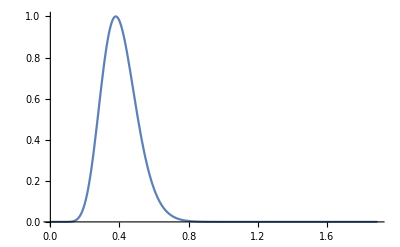

lower 2.29083×10^-9

upper 6.27422×10^-9

{13.3281,Null}

```mathematica
Clear[logp]
logp[μ_?NumberQ]:=logp[μ]=Sum[Module[{p,m=tmp[[kk,2]] μ},p[0]=Exp[-m];
p[n_]:=p[n]=m/n Sum[p[i]/(n-i+1),{i,0,n-1}];
Total[Log[p[#]&/@tmp[[kk,3]]]]],{kk,Length[tmp]}];
μguess=Sort[Table[{logp[μ0],μ0}/.μ0->10^x,{x,-10,-8,0.2}]][[-1,2]]
Timing[Module[{fm=FindMaximum[logp[μ],{μ,0.5μguess,1.5μguess}],mumax,norm,dμ,mean,x,tot},mumax=μ/.fm[[2]];Print["maximum at ",mumax];
dμ=mumax/500;
norm=Sum[Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}];
Print[norm];
mean=Sum[μ Exp[logp[μ]-fm[[1]]],{μ,0.001mumax,10mumax,dμ}]/norm;Print["mean μ=",mean];
Print[Plot[Exp[logp[μ]-fm[[1]]],{μ,10^-11,5mumax},PlotRange->All]];
x=0.001mumax;tot=0;While[tot<0.025(norm),tot+=Exp[logp[x]-fm[[1]]];x+=dμ];
Print["lower ",x];
While[tot<0.975(norm),tot+=Exp[Max[-100,logp[x]-fm[[1]]]];x+=dμ];
Print["upper ",x];
]]
```

### The rate that will be used for STR mutS simulations: μ = 4.0 x 10^-9

## Import turbidostat data

### This imports all experimental data pre - processed before by process_data.nb

```mathematica
<<("turb_rif_long_runs_ODvsTIME.mx");
dataRIFlong=data;  (* uncorrected data *)
Length[dataRIFlong]
<<("turb_rif_long_runs_ODvsTIME_corrected.mx");
dataRIFlongcorrected=data; (* corrected data *)

<<("turb_cip_long_runs_ODvsTIME.mx");
dataCIPlong=data;
Length[dataCIPlong]
<<("turb_str_long_runs_ODvsTIME.mx");
dataSTRlong=data;
Length[dataSTRlong]
<<("turb_str_mutS_long_runs_ODvsTIME.mx");
dataSTRmutSlong=data;
Length[dataSTRmutSlong]

<<("turb_rif_long_runs.mx");
paramsRIFlong=alldata;
<<("turb_cip_long_runs.mx");
paramsCIPlong=alldata;
<<("turb_str_long_runs.mx");
paramsSTRlong=alldata;
<<("turb_str_mutS_long_runs.mx");
paramsSTRmutSlong=alldata;

<<("turb_rif_short_runs.mx");
paramsRIFshort=alldata;
Print[Length[paramsRIFshort]]
<<("turb_cip_short_runs.mx");
paramsCIPshort=alldata;
Print[Length[paramsCIPshort]]
<<("turb_str_short_runs.mx");
paramsSTRshort=alldata;
Print[Length[paramsSTRshort]]

<<("turb_rif_short_runs_ODvsTIME.mx")
dataRIFshort=data;


<<("turb_cip_long_runs_growthrates.mx");
growthratesCIP=growthrates;
<<("turb_rif_long_runs_growthrates.mx");
growthratesRIF=growthrates;
<<("turb_str_long_runs_growthrates.mx");
growthratesSTR=growthrates;
```

23

32

24

4

5

5

5

## Figure 1

### figure 1B

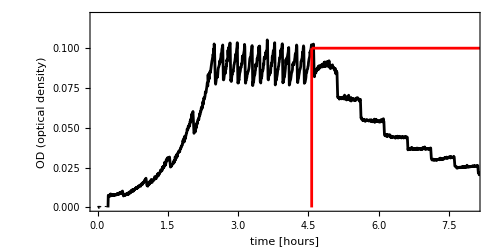

figures\example_data.png

```mathematica
ListPlot[dataRIFlong[[4,"ods"]],PlotStyle->Black,Joined->True,Frame->True,PlotRange->{{0,8},{0,0.12}},AspectRatio->0.5,ImageSize->500,BaseStyle->FontSize->24,FrameLabel->{"time [hours]","OD (optical density)"},Epilog->{Red,AbsoluteThickness[2],Line[{{t,0},{t,0.1}}],Line[{{t,0.1},{10,0.1}}]}/.t->dataRIFlong[[4,"Ainjs",1,1]]]
Export["figures\\example_data.png",%,"PNG"]
```

### figure 1C - RIF

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsRIFlong;
```

```mathematica
valid=(Position[birthsres[[All,1]],#]&/@Select[birthsres[[All,1]],(NumberQ[#] && Abs[#]<2)&])[[All,1,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,20,21,22,23}

```mathematica
colors=(Hue[0.3+0.4(#-Min[tregrowths])/(Max[tregrowths]-Min[tregrowths])]&/@tregrowths)
```

{Hue[0.47704759583637973],Hue[0.49175399895430394],Hue[0.4494812139240058],Hue[0.46580657122086067],Hue[0.42989461799805445],Hue[0.35725831817907233],Hue[0.3885000510349683],Hue[0.4024773831767914],Hue[0.44372530272068456],Hue[0.5093200267464895],Hue[0.5085851232025796],Hue[0.44852300635541587],Hue[0.4471531861443184],Hue[0.4349889493670622],Hue[0.5211101459600094],Hue[0.4530815747099859],Hue[0.5947379823064889],Hue[0.7],Hue[0.37105984006265846],Hue[0.3664604437334267],Hue[0.5033166480232802],Hue[0.3],Hue[0.40131503573489313]}

```mathematica
(* alternative version which subtracts bkg as done for model comparison *)
(*ListPlot[Table[bkgcorr={0,#[[2]]-dataRIFlong[[k,"odbkg",1,2]]}&/@dataRIFlong[[k,"odbkg"]];RemoveSpikes[({#[[1]]-dataRIFlong[[k,"Ainjs",1,1]],#[[2]]}&/@dataRIFlong[[k,"ods"]])+bkgcorr],{k,Length[dataRIFlong]}],Joined->True,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->24,AspectRatio->0.3,ImageSize->{Automatic,250},Axes->False,Epilog->{Red,Thick,Line[{{0,0},{0,3}}]},PlotRange->{0,0.14},PlotStyle->colors]
Export["paper_3ABs\\RIF_all_exprs.png",%,"PNG"]*)
```

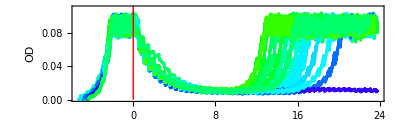

figures\RIF_all_exprs.png

```mathematica
(* this version does not substract the RIF contribution *)
ListPlot[Table[RemoveSpikes[({#[[1]]-dataRIFlong[[k,"Ainjs",1,1]],#[[2]]}&/@dataRIFlong[[k,"ods"]])],{k,Length[dataRIFlong]}],Joined->True,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->24,AspectRatio->0.3,ImageSize->{Automatic,250},Axes->False,Epilog->{Red,Thick,Line[{{0,0},{0,3}}]},PlotRange->{0,0.11},PlotStyle->colors]
Export["figures\\RIF_all_exprs.png",%,"PNG"]
```

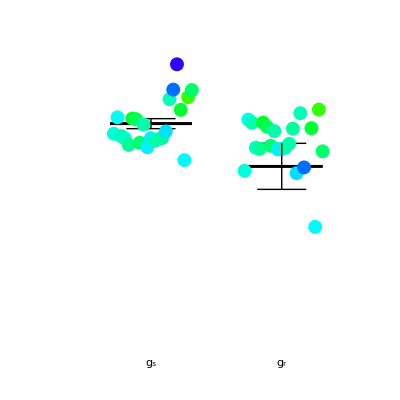

figures\RIF_grrates.png

```mathematica
Clear[MakeBar]
colors=(Hue[0.3+0.4(#-Min[paramsRIFlong[[6]]])/(Max[paramsRIFlong[[6]]]-Min[paramsRIFlong[[6]]])]&/@paramsRIFlong[[6]]);
MakeBar[x_,data_]:={AbsolutePointSize[10],Table[{colors[[valid]][[i]],Point[{x+(i/Length[data]-0.5)0.5,data[[i]]}]},{i,Length[data]}],AbsoluteThickness[2],Line[{{x-0.25,y},{x+0.25,y}}],Line[{{x-0.25,y},{x+0.25,y}}],AbsoluteThickness[1],Line[{{x-0.15,y-sy},{x+0.15,y-sy}}],Line[{{x-0.15,y+sy},{x+0.15,y+sy}}],Line[{{x,y-sy},{x,y+sy}}]}/.{y->Mean[data],sy->SE[data]};
Graphics[{MakeBar[0.7,births[[valid,1]]],MakeBar[1.5,birthsres[[valid,1]]]},Epilog->{Text["g_s",{0.7,1.0}],Text["g_r",{1.5,1.0}]},Axes->{None,Automatic},PlotRange->{{0,2},{1.0,2.2}},Axes->True,AspectRatio->1,BaseStyle->FontSize->24,ImageSize->{Automatic,200}]
Export["figures\\RIF_grrates.png",%,"PNG"]
```

### figure 1D - CIP

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsCIPlong;
```

```mathematica
valid=(Position[birthsres[[All,1]],#]&/@Select[birthsres[[All,1]],(NumberQ[#] && Abs[#]<2 && Abs[#]>0)&])[[All,1,1]]
```

{2,5,6,7,9,10,12,14,19,20,24,25,27,28,32}

```mathematica
colors=(Hue[0.3+0.4(#-Min[tregrowths])/(Max[tregrowths]-Min[tregrowths])]&/@tregrowths)
```

{Hue[0.7],Hue[0.4253433291158699],Hue[0.7],Hue[0.7],Hue[0.366207712045785],Hue[0.42148565077037686],Hue[0.4490380635930423],Hue[0.5877243434355378],Hue[0.4139793541368586],Hue[0.5062306518937199],Hue[0.594071823008431],Hue[0.4070737504286441],Hue[0.647583629935319],Hue[0.4424853078551242],Hue[0.6475930896664261],Hue[0.6475930896664261],Hue[0.6460227743026404],Hue[0.6460227743026404],Hue[0.4824763211105725],Hue[0.34386098925138053],Hue[0.6734370750511416],Hue[0.6734370750511416],Hue[0.6734370750511416],Hue[0.4906599344913621],Hue[0.6080807388049995],Hue[0.6368373753976044],Hue[0.40084830138703315],Hue[0.3],Hue[0.6547257269212123],Hue[0.6547257269212123],Hue[0.6547257269212123],Hue[0.5609447906443259]}

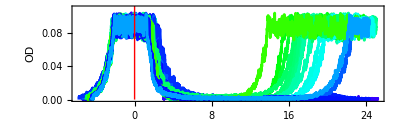

figures\CIP_all_exprs.png

```mathematica
ListPlot[Table[{#[[1]]-dataCIPlong[[k,"Ainjs",1,1]],#[[2]]}&/@RemoveSpikes[dataCIPlong[[k,"ods"]]],{k,Length[dataCIPlong]}],Joined->True,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->24,AspectRatio->0.3,ImageSize->{Automatic,250},Axes->False,Epilog->{Red,Thick,Line[{{0,0},{0,3}}]},PlotRange->{0,0.11},PlotStyle->colors]
Export["figures\\CIP_all_exprs.png",%,"PNG"]
```

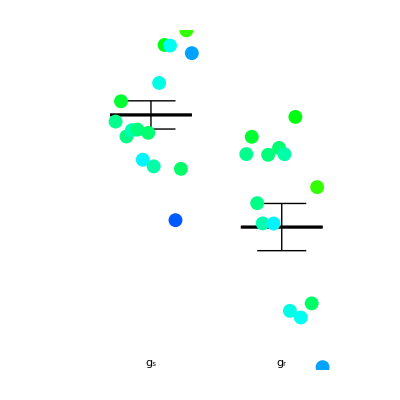

figures\CIP_grrates.png

```mathematica
Clear[MakeBar]
colors=(Hue[0.3+0.4(#-Min[paramsCIPlong[[6]]])/(Max[paramsCIPlong[[6]]]-Min[paramsCIPlong[[6]]])]&/@paramsCIPlong[[6]])[[valid]];
MakeBar[x_,data_]:={AbsolutePointSize[10],Table[{colors[[i]],Point[{x+(i/Length[data]-0.5)0.5,data[[i]]}]},{i,Length[data]}],AbsoluteThickness[2],Line[{{x-0.25,y},{x+0.25,y}}],Line[{{x-0.25,y},{x+0.25,y}}],AbsoluteThickness[1],Line[{{x-0.15,y-sy},{x+0.15,y-sy}}],Line[{{x-0.15,y+sy},{x+0.15,y+sy}}],Line[{{x,y-sy},{x,y+sy}}]}/.{y->Mean[data],sy->SE[data]};
Graphics[{MakeBar[0.7,births[[valid,1]]],MakeBar[1.5,birthsres[[valid,1]]]},Epilog->{Text["g_s",{0.7,1.4}],Text["g_r",{1.5,1.4}]},Axes->{None,Automatic},PlotRange->{{0,2},{1.4,2}},Axes->True,AspectRatio->1,BaseStyle->FontSize->24,ImageSize->{Automatic,200}]
Export["figures\\CIP_grrates.png",%,"PNG"]
```

### figure 1E - STR

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsSTRlong;
```

```mathematica
valid=(Position[birthsres[[All,1]],#]&/@Select[birthsres[[All,1]],(NumberQ[#] && Abs[#]<3 && #>0)&])[[All,1,1]]
```

{1,5,8}

```mathematica
colors=(Hue[0.3+0.4(#-Min[tregrowths])/(Max[tregrowths]-Min[tregrowths])]&/@tregrowths)
```

{Hue[0.4581538932348946],Hue[0.5731495897328003],Hue[0.5731511198668783],Hue[0.5731526500009564],Hue[0.5072972094179753],Hue[0.523746915823499],Hue[0.5237484459575771],Hue[0.3],Hue[0.5463095078706272],Hue[0.5463110380047052],Hue[0.5463125681387832],Hue[0.5463140982728611],Hue[0.6583650517376585],Hue[0.6583650517376585],Hue[0.6583650517376585],Hue[0.6583727024080486],Hue[0.6092951819903218],Hue[0.6092959470573609],Hue[0.6092974771914389],Hue[0.6092990073255169],Hue[0.6999923493296101],Hue[0.6999923493296101],Hue[0.7],Hue[0.7]}

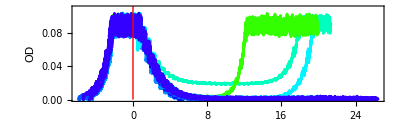

figures\STR_all_exprs.png

```mathematica
ListPlot[Table[{#[[1]]-dataSTRlong[[k,"Ainjs",1,1]],#[[2]]}&/@RemoveSpikes[dataSTRlong[[k,"ods"]]],{k,Length[dataSTRlong]}],Joined->True,Frame->True,FrameLabel->{"t-t_0 [h]","OD"},BaseStyle->FontSize->24,AspectRatio->0.3,ImageSize->{Automatic,250},Axes->False,Epilog->{Red,Thick,Line[{{0,0},{0,3}}]},PlotRange->{0,0.11},PlotStyle->colors]
Export["figures\\STR_all_exprs.png",%,"PNG"]
```

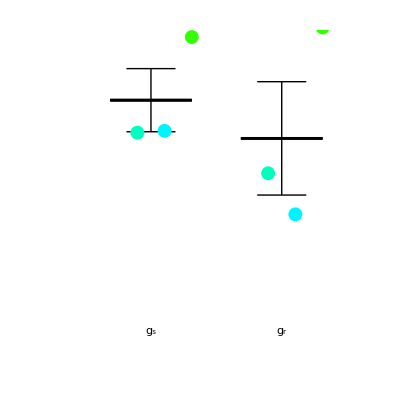

figures\STR_grrates.png

```mathematica
Clear[MakeBar]
colors=(Hue[0.3+0.4(#-Min[paramsSTRlong[[6]]])/(Max[paramsSTRlong[[6]]]-Min[paramsSTRlong[[6]]])]&/@paramsSTRlong[[6]])[[valid]];
MakeBar[x_,data_]:={AbsolutePointSize[10],Table[{colors[[i]],Point[{x+(i/Length[data]-0.5)0.5,data[[i]]}]},{i,Length[data]}],AbsoluteThickness[2],Line[{{x-0.25,y},{x+0.25,y}}],Line[{{x-0.25,y},{x+0.25,y}}],AbsoluteThickness[1],Line[{{x-0.15,y-sy},{x+0.15,y-sy}}],Line[{{x-0.15,y+sy},{x+0.15,y+sy}}],Line[{{x,y-sy},{x,y+sy}}]}/.{y->Mean[data],sy->SE[data]};
Graphics[{MakeBar[0.7,births[[valid,1]]],MakeBar[1.5,birthsres[[valid,1]]]},Epilog->{Text["g_s",{0.7,1.1}],Text["g_r",{1.5,1.1}]},Axes->{None,Automatic},PlotRange->{{0,2},{1.0,2}},Axes->True,AspectRatio->1,BaseStyle->FontSize->24,ImageSize->{Automatic,200}]
Export["figures\\STR_grrates.png",%,"PNG"]
```

## Figure 2A,B

### The model assumes that OD = 0.1 corresponds to 2x 10^7 cells/ml.

```mathematica
th=Import["models\\turbidostat_example\\turbidostat_example_bs_2.0_br_1.5_n=0.dat","Table"];
```

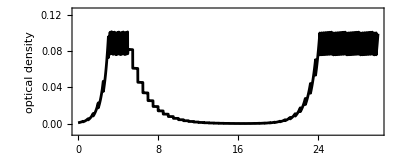

```mathematica
ListPlot[th[[All,{1,5}]],PlotRange->{-0.01,0.125},Joined->True,AspectRatio->0.4,ImageSize->{Automatic,300},FrameLabel->{"t [hours]","optical density"},PlotStyle->Black]
```

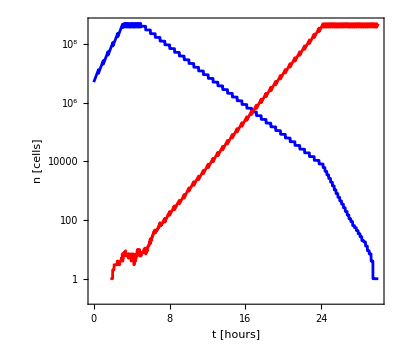

figures\model_demo.png

```mathematica
ListLogPlot[{th[[All,{1,2}]],th[[All,{1,3}]]},PlotRange->All,Joined->True,AspectRatio->0.9,ImageSize->{Automatic,300},FrameLabel->{"t [hours]","n [cells]"},PlotStyle->{Blue,Red}]
Export["figures\\model_demo.png",%,"PNG"]
```

## Figure 2 C

### RIF. We chose experimental replicate 23 for this plot.

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsRIFlong;
```

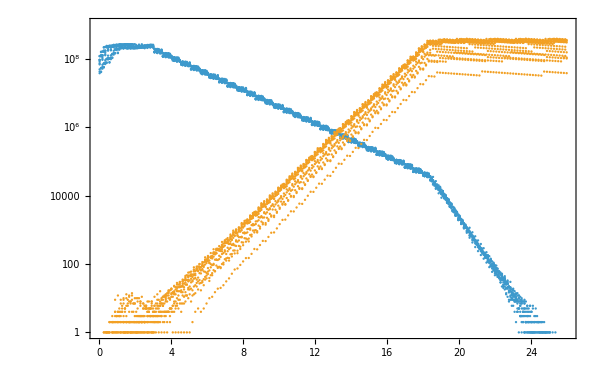

```mathematica
kk=23;
nns=ReadList["models\\RIF\\n_fixed_mu_2strains_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[;;;;10,{1,2}]],nns[[;;;;10,{1,3}]]},ImageSize->600,PlotRange->{1,10^9}]
th=Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[i]]];If[i==Length[nns] || nns[[i+1,1]]<nns[[i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns]}];th];
```

17

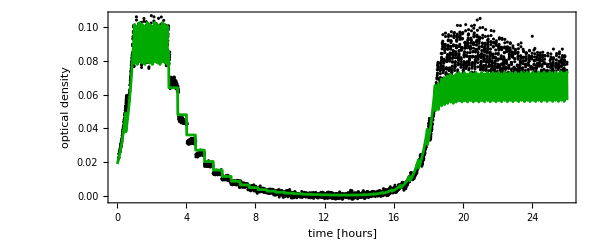

figures\RIF_model_and_expr_example.png

```mathematica
(* find a theoretical curve that best fits this specific experiment and superimpose it on the data *)
bestfiti=Ordering[Table[Module[{ii=1},Do[If[th[[k,i,6]]>0.1,ii=i;Break[]],{i,Length[th[[k]]]}];Abs[th[[k,ii,1]]-tfirstthr[[kk]]]],{k,Length[th]}]][[1]]
Show[ListPlot[dataRIFlongcorrected[[kk,"ods"]],PlotRange->All,PlotStyle->Black],ListPlot[th[[bestfiti,All,{1,6}]],PlotRange->{0,0.12},Joined->True,PlotStyle->Darker[Green]],AspectRatio->0.4,ImageSize->600,FrameLabel->{"time [hours]","optical density"}]
Export["figures\\RIF_model_and_expr_example.png",%,"PNG"]
```

### CIP. We chose experimental replicate 28 for this plot.

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsCIPlong;
```

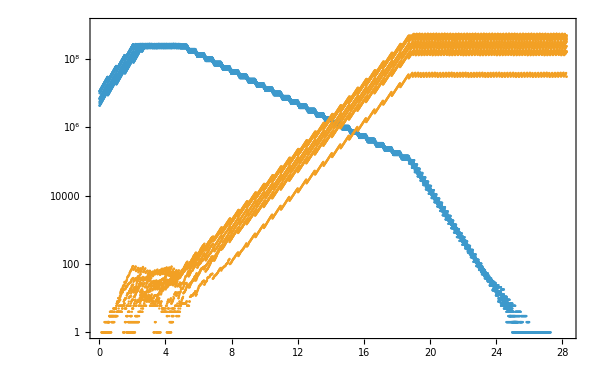

```mathematica
kk=28;
nns=ReadList["models\\CIP\\n_fixed_mu_2strains_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[All,{1,2}]],nns[[All,{1,3}]]},ImageSize->600,PlotRange->{1,10^9}]
th=Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[i]]];If[i==Length[nns] || nns[[i+1,1]]<nns[[i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns]}];th];
```

10

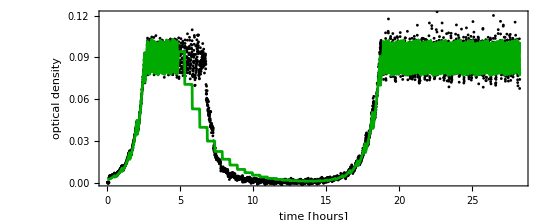

figures\CIP_model_and_expr_example.png

```mathematica
bestfiti=Ordering[Table[Module[{ii=1},Do[If[th[[k,i,6]]>0.1,ii=i;Break[]],{i,Length[th[[k]]]}];Abs[th[[k,ii,1]]-tfirstthr[[kk]]]],{k,Length[th]}]][[1]]
bestfitCIP=th[[bestfiti,All,{1,6}]];
Show[ListPlot[dataCIPlong[[kk,"ods"]],PlotRange->{0,0.121},PlotStyle->Black],ListPlot[th[[bestfiti,All,{1,6}]],Joined->True,PlotStyle->Darker[Green]],AspectRatio->0.40,ImageSize->550,FrameLabel->{"time [hours]","optical density"}]
Export["figures\\CIP_model_and_expr_example.png",%,"PNG"]
```

### STR. We chose experimental replicate 8 for this plot.

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsSTRlong;
```

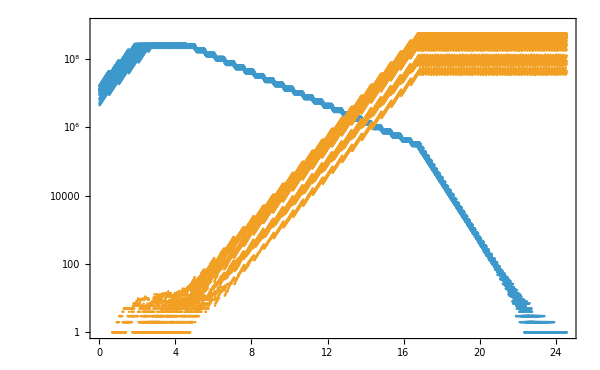

```mathematica
kk=8;
nns=ReadList["models\\STR\\n_fixed_mu_2strains_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[All,{1,2}]],nns[[All,{1,3}]]},ImageSize->600,PlotRange->{1,10^9}]
th=Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[i]]];If[i==Length[nns] || nns[[i+1,1]]<nns[[i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns]}];th];
```

8

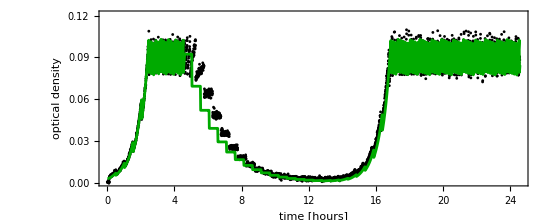

figures\STR_model_and_expr_example.png

```mathematica
bestfiti=Ordering[Table[Module[{ii=1},Do[If[th[[k,i,6]]>0.1,ii=i;Break[]],{i,Length[th[[k]]]}];Abs[th[[k,ii,1]]-tfirstthr[[kk]]]],{k,Length[th]}]][[1]]
bestfitSTR=th[[bestfiti,All,{1,6}]];
Show[ListPlot[dataSTRlong[[kk,"ods"]],PlotRange->{0,0.121},PlotStyle->Black],ListPlot[th[[bestfiti,All,{1,6}]],Joined->True,PlotStyle->Darker[Green]],AspectRatio->0.40,ImageSize->550,FrameLabel->{"time [hours]","optical density"}]
Export["figures\\STR_model_and_expr_example.png",%,"PNG"]
```

## Figure S3 AB

### CIP. We chose experimental replicate 5 for this plot.

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsCIPlong;
```

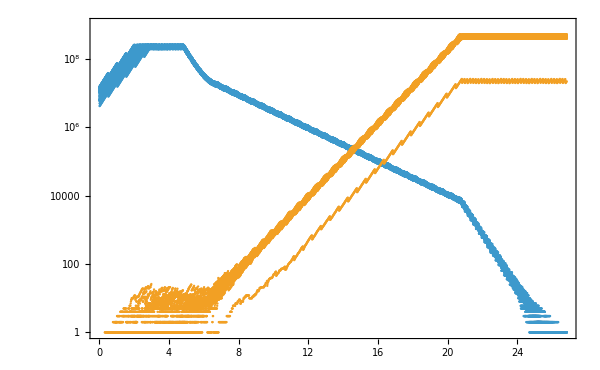

```mathematica
kk=5;
nns=ReadList["models\\CIP_filament\\n_fixed_mu_2strains_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[All,{1,2}]],nns[[All,{1,3}]]},ImageSize->600,PlotRange->{1,10^9}]
th=Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[i]]];If[i==Length[nns] || nns[[i+1,1]]<nns[[i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns]}];th];
```

7

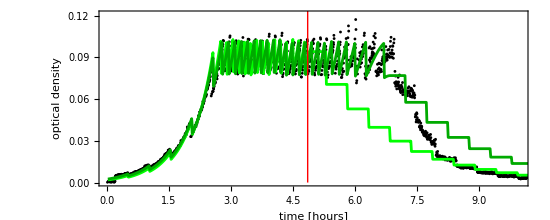

figures\CIP_filam_model_and_expr_example.png

```mathematica
bestfiti=Ordering[Table[Module[{ii=1},Do[If[th[[k,i,6]]>0.1,ii=i;Break[]],{i,Length[th[[k]]]}];Abs[th[[k,ii,1]]-tfirstthr[[kk]]]],{k,Length[th]}]][[1]]
Show[ListPlot[dataCIPlong[[kk,"ods"]],PlotRange->{{0,10},{0,0.121}},PlotStyle->Black],ListPlot[{bestfitCIP,th[[bestfiti,All,{1,6}]]},Joined->True,PlotStyle->{Green,Darker[Green]}],AspectRatio->0.40,ImageSize->550,FrameLabel->{"time [hours]","optical density"},Epilog->{Red,Thick,Line[{{ainjs[[kk]],0},{ainjs[[kk]],3}}]}]
Export["figures\\CIP_filam_model_and_expr_example.png",%,"PNG"]
```

### STR. We chose experimental replicate 8 for this plot.

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsSTRlong;
```

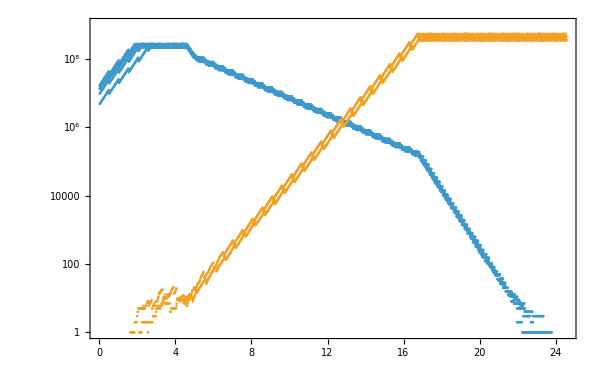

```mathematica
kk=8;
nns=ReadList["models\\STR_filament_fitted\\n_fixed_mu_2strains_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[All,{1,2}]],nns[[All,{1,3}]]},ImageSize->600,PlotRange->{1,10^9}]
th=Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[i]]];If[i==Length[nns] || nns[[i+1,1]]<nns[[i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns]}];th];
```

5

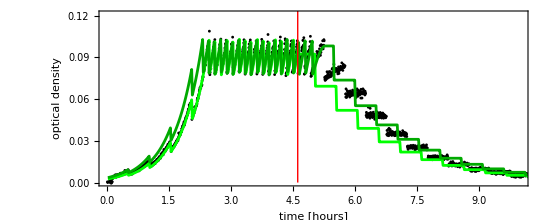

figures\STR_filam_model_and_expr_example.png

```mathematica
bestfiti=Ordering[Table[Module[{ii=1},Do[If[th[[k,i,6]]>0.1,ii=i;Break[]],{i,Length[th[[k]]]}];Abs[th[[k,ii,1]]-tfirstthr[[kk]]]],{k,Length[th]}]][[1]]
Show[ListPlot[dataSTRlong[[kk,"ods"]],PlotRange->{{0,10},{0,0.121}},PlotStyle->Black],ListPlot[{bestfitSTR,th[[bestfiti,All,{1,6}]]},Joined->True,PlotStyle->{Green,Darker[Green]}],AspectRatio->0.40,ImageSize->550,FrameLabel->{"time [hours]","optical density"},Epilog->{Red,Thick,Line[{{ainjs[[kk]],0},{ainjs[[kk]],3}}]}]
Export["figures\\STR_filam_model_and_expr_example.png",%,"PNG"]
```

## Figure 3A

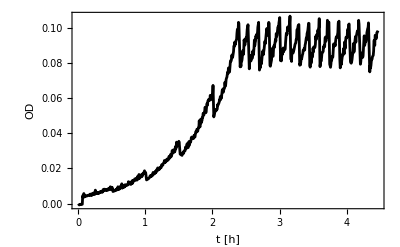

```mathematica
ListPlot[dataRIFshort[[1,"ods"]],Joined->True,PlotStyle->Black,FrameLabel->{"t [h]","OD"}]
Export["figures\\RIF_short_term_example.png",%,"PNG"]
```

## Supplementary Table 1

```mathematica
<<"CIP_mult_alleles.mx"
<<"CIP_mult_alleles_probs.mx"
allrates2=allrates;
mutprobs2=mutprobs;
```

```mathematica
<<"RIF_mult_alleles.mx"
<<"RIF_mult_alleles_probs.mx"
```

```mathematica
allrates
```

{{rpoB S512P,1.77465,1.43415},{rpoB S512F,1.80241,1.5536},{rpoB D516Y,1.99908,2.03764},{rpoB T563P,1.68159,0.76101},{rpoB H526Y,1.88764,1.91346},{rpoB G534D,1.28577,0.513987},{rpoB R454P,1.19505,0.499673},{rpoB I572L,1.71817,1.07787},{rpoB Q148L,1.81943,0.874744},{rpoB H526D,1.84011,1.86566},{rpoB D516G,1.86841,1.43485},{rpoB I572S,1.9491,1.13081},{rpoB H526L,2.16938,2.16552},{rpoB R529C,0.565199,0.625219},{rpoB Q513P,1.23712,1.38641},{rpoB S531F,1.70002,1.73611},{rpoB G534V,1.78559,0.735189},{rpoB Q513L,1.71756,1.88525},{rpoB H526N,1.90167,1.96703},{rpoB S531Y,1.6161,1.73519},{rpoB P564L,1.59997,1.6746}}

```mathematica
mutantorigin=Import["mutation_summary_turbidostat.xlsx","XLSX"][[1,2;;]];
mutantgrowthrates=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1,2;;]];
nosdetected=mutantorigin[[Position[mutantorigin,#][[1,1]]]][[2;;3]]&/@mutantgrowthrates[[4;;,3]];
RIFcomments=Table[If[nosdetected[[i,1]]>0,If[nosdetected[[i,2]]>0,"long- and short-term experiment","short-term experiment"],"long-term experiment"],{i,21}]
```

{long- and short-term experiment,short-term experiment,long- and short-term experiment,short-term experiment,long- and short-term experiment,short-term experiment,short-term experiment,short-term experiment,short-term experiment,long- and short-term experiment,long- and short-term experiment,short-term experiment,long- and short-term experiment,short-term experiment,short-term experiment,long- and short-term experiment,short-term experiment,long-term experiment,long-term experiment,long-term experiment,long-term experiment}

```mathematica
mutantorigin=Import["mutation_summary_turbidostat.xlsx","XLSX"][[2,2;;]];
mutantgrowthrates=Import["CipR_mutants_turb_growth_summary.xlsx","XLSX"][[1,2;;]];
nosdetected=(mutantorigin[[Position[mutantorigin,#][[1,1]]]][[2;;3]])&/@mutantgrowthrates[[4;;,3]];
CIPcomments=Table[If[nosdetected[[i,1]]>0,If[nosdetected[[i,2]]>0,"long- and short-term experiment","short-term experiment"],"long-term experiment"],{i,9}]
```

{long-term experiment,short-term experiment,long- and short-term experiment,long-term experiment,long-term experiment,long- and short-term experiment,short-term experiment,short-term experiment,short-term experiment}

```mathematica
MatrixForm[Join[{{"antibiotic","mutation","growth rate (LB) [h^-1]","growth rate (antibiotic) [h^-1]","relative mutation frequency","comments"}},Table[Join[{"RIF"},allrates[[i]],{mutprobs[[i,2]],RIFcomments[[i]]}],{i,Length[allrates]}],Table[Join[{"CIP"},allrates2[[i]],{mutprobs2[[i,2]],CIPcomments[[i]]}],{i,Length[allrates2]}],{{"STR","hemB deletion","NA","NA","","small colonies on agar plate from short-term experiment, not observed in populations evolved in the bioreactor"},
{"STR","rpsL K43R","1.71","1.76","","normal-size colonies, short-term experiment"},(*
{"STR","rpsL G92D","","","","normal-size colonies, mutS strain, short-term experiment"},*)
{"STR","rpsL K43T","1.54","1.54","","normal-size colonies, long-term experiment"},(*
{"STR","rpsL K88E","","","","normal-size colonies, short-term (mutS strain)"},*)
{"STR","rpsL K88R","1.96","1.86","","normal-size colonies, long-term experiment"}(*,
{"STR","rpsL KP91L","","","","normal-size colonies, short-term (mutS strains)"}*)}]]
Export["SI_Table_1.xlsx",%,"XLSX"]
```

(antibiotic | mutation | growth rate (LB) [h^-1] | growth rate (antibiotic) [h^-1] | relative mutation frequency | comments
RIF | rpoB S512P | 1.77465 | 1.43415 | 0.21 | long- and short-term experiment
RIF | rpoB S512F | 1.80241 | 1.5536 | 0.35 | short-term experiment
RIF | rpoB D516Y | 1.99908 | 2.03764 | 0.13 | long- and short-term experiment
RIF | rpoB T563P | 1.68159 | 0.76101 | 0.16 | short-term experiment
RIF | rpoB H526Y | 1.88764 | 1.91346 | 0.35 | long- and short-term experiment
RIF | rpoB G534D | 1.28577 | 0.513987 | 0.35 | short-term experiment
RIF | rpoB R454P | 1.19505 | 0.499673 | 0.07 | short-term experiment
RIF | rpoB I572L | 1.71817 | 1.07787 | 0.16 | short-term experiment
RIF | rpoB Q148L | 1.81943 | 0.874744 | 0.07 | short-term experiment
RIF | rpoB H526D | 1.84011 | 1.86566 | 0.07 | long- and short-term experiment
RIF | rpoB D516G | 1.86841 | 1.43485 | 0.21 | long- and short-term experiment
RIF | rpoB I572S | 1.9491 | 1.13081 | 0.16 | short-term experiment
RIF | rpoB H526L | 2.16938 | 2.16552 | 0.07 | long- and short-term experiment
RIF | rpoB R529C | 0.565199 | 0.625219 | 0.35 | short-term experiment
RIF | rpoB Q513P | 1.23712 | 1.38641 | 0.16 | short-term experiment
RIF | rpoB S531F | 1.70002 | 1.73611 | 0.35 | long- and short-term experiment
RIF | rpoB G534V | 1.78559 | 0.735189 | 0.13 | short-term experiment
RIF | rpoB Q513L | 1.71756 | 1.88525 | 0.07 | long-term experiment
RIF | rpoB H526N | 1.90167 | 1.96703 | 0.13 | long-term experiment
RIF | rpoB S531Y | 1.6161 | 1.73519 | 0.13 | long-term experiment
RIF | rpoB P564L | 1.59997 | 1.6746 | 0.35 | long-term experiment
CIP | gyrA D87N | 1.91654 | 1.43438 | 0.35 | long-term experiment
CIP | gyrA G81D | 1.66216 | 1.23893 | 0.35 | short-term experiment
CIP | gyrA D87Y | 1.85083 | 1.53978 | 0.13 | long- and short-term experiment
CIP | gyrA D87G | 1.98136 | 1.39731 | 0.21 | long-term experiment
CIP | gyrB S464F | 1.83286 | 1.05029 | 0.35 | long-term experiment
CIP | gyrB G429V | 1.24441 | 1.12944 | 0.13 | long- and short-term experiment
CIP | gyrB S463P | 1.62962 | 1.763 | 0.21 | short-term experiment
CIP | gyrA S111Y | 1.85954 | 0.876618 | 0.13 | short-term experiment
CIP | gyrA S83L | 1.84706 | 1.67539 | 0.35 | short-term experiment
STR | hemB deletion | NA | NA |  | small colonies on agar plate from short-term experiment, not observed in populations evolved in the bioreactor
STR | rpsL K43R | 1.71 | 1.76 |  | normal-size colonies, short-term experiment
STR | rpsL K43T | 1.54 | 1.54 |  | normal-size colonies, long-term experiment
STR | rpsL K88R | 1.96 | 1.86 |  | normal-size colonies, long-term experiment)

SI_Table_1.xlsx

## Figure S2 - growth rates vs time

### CIP

{0,1.78423,0,0,1.81596,1.69421,1.65712,0,1.78294,1.65685,0,1.79557,0,1.78415,0,0,0,0,1.49658,1.85249,0,0,0,1.48436,1.32328,0,1.51023,1.72362,0,0,0,1.39317}

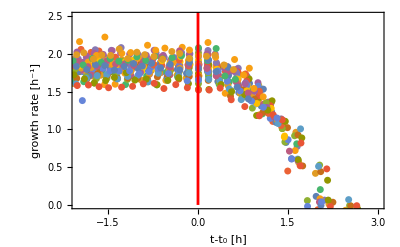

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsCIPlong;
birthsres[[All,1]]
ListPlot[Table[{#[[1]]-ainjs[[k]],#[[2]]}&/@RemoveSpikes[growthratesCIP[[k]],1],{k,Length[vols]}],PlotRange->{{-2,3},{0,2.5}},PlotStyle->AbsolutePointSize[5],FrameLabel->{"t-t_0 [h]","growth rate [h^-1]"},Axes->False,Epilog->{Red,AbsoluteThickness[2],Line[{{0,0},{0,3}}]}]
Export["figures\\CIP_growth_response.png",%,"PNG"]
```

### STR

{1.58172,0,0,0,1.45615,0,0,2.0276,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

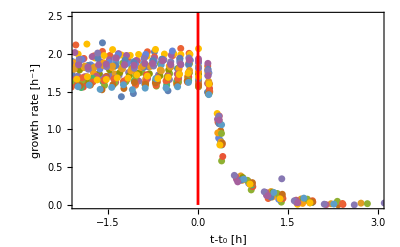

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsSTRlong;
birthsres[[All,1]]
ListPlot[Table[{#[[1]]-ainjs[[k]],#[[2]]}&/@RemoveSpikes[growthratesSTR[[k]],1],{k,Length[vols]}],PlotRange->{{-2,3},{0,2.5}},PlotStyle->AbsolutePointSize[5],FrameLabel->{"t-t_0 [h]","growth rate [h^-1]"},Axes->False,Epilog->{Red,AbsoluteThickness[2],Line[{{0,0},{0,3}}]}]
Export["figures\\STR_growth_response.png",%,"PNG"]
```

### RIF

{1.70686,1.89509,1.88363,1.79217,1.7878,1.88392,1.86912,1.79884,1.85305,1.7858,1.78783,1.79198,1.80611,1.86198,1.69856,1.91859,1.71954,0,2.26897,1.86358,1.50135,1.93188,1.77871}

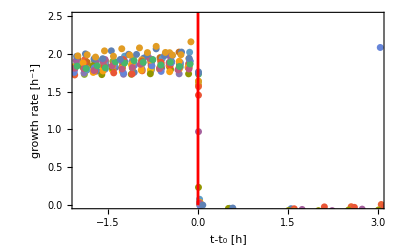

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsRIFlong;
birthsres[[All,1]]
ListPlot[Table[{#[[1]]-ainjs[[k]],#[[2]]}&/@growthratesRIF[[k]],{k,17}],PlotRange->{{-2,3},{0,2.5}},PlotStyle->AbsolutePointSize[5],FrameLabel->{"t-t_0 [h]","growth rate [h^-1]"},Axes->False,Epilog->{Red,AbsoluteThickness[2],Line[{{0,0},{0,3}}]}]
Export["figures\\RIF_growth_response.png",%,"PNG"]
```